```mathematica
Clear["Global `*"];
rule1 ={ϵ -> 78*10^3} ;
```

```mathematica
K[x1_, x2_] := (Cos[x1]^2-Cos[x2])/2
```

```mathematica
K[0,Pi/2]
```

1/2

```mathematica
Q(x1_,x2_):=(1/8 (1-2 x1^2) cos(2 x1)+2 x1 sin(2 x1))-(1/8 (1-2 x2^2) cos(2 x2)+2 x2 sin(2 x2))
```

```mathematica
N[Q[0,Pi/2]]
```

```mathematica
-0.3668502750680849
```

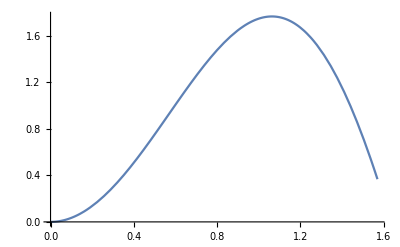

```mathematica
Plot[Q[x,0],{x,0,Pi/2}]
```

```mathematica
ConcentrationFunc1[x_,d_,y1_,y2_]:=N[Log[x/(2 K[y1,y2])]/(78 10^3 d Log[1/10^2])]
```

```mathematica
ScientificForm[ConcentrationFunc1[.5,30,0,Pi/2]]
```

6.43226×10^-8

```mathematica
ConcentrationFunc1[.5,20,0,Pi/3]
```

0.

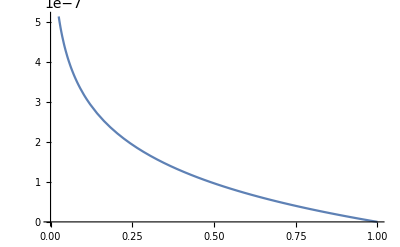

```mathematica
Plot[N[ConcentrationFunc1[x,20,0,Pi/2]],{x,0,1}]
```

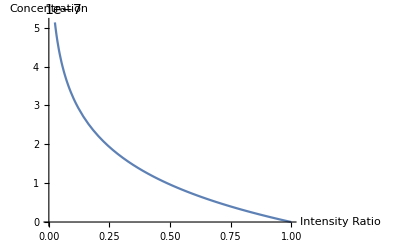

```mathematica
Show[%116,AxesLabel->{HoldForm[Intensity Ratio],HoldForm[Concentration]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
ConcentrationFunc2[x_,d_,y1_,y2_]:=N[Log[x/(2K[y1,y2])]/((78 10^3 d) (- 2*Q[y1,y2]-Log[10^2]))]
```

```mathematica
ScientificForm[ConcentrationFunc2[1,30,0,Pi/2]]
```

0.

```mathematica
Plot[ConcentrationFunc2[x,20,0,Pi/2], {x,0,1}, PlotLegends -> "Expressions"]
```

Plot[ConcentrationFunc2[x,20,0,π/2],{x,0,1},PlotLegends→Expressions]

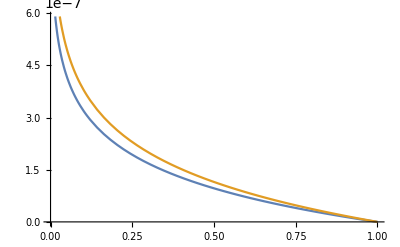

```mathematica
Plot[{ConcentrationFunc1[x,20,0,Pi/2],ConcentrationFunc2[x,20,0,Pi/2]},{x,0,1}]
```

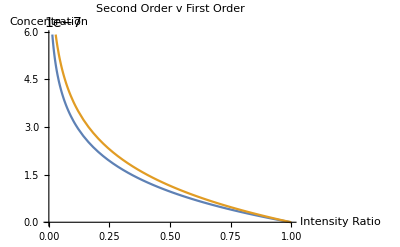

```mathematica
Show[%175,AxesLabel->{HoldForm[Intensity Ratio],HoldForm[Concentration]},PlotLabel->HoldForm[Second Order v First Order],LabelStyle->{GrayLevel[0]}]
```